-Graphics3D-

-Graphics3D-

-Graphics3D-

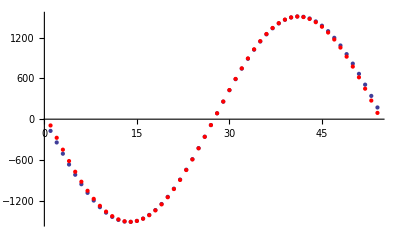

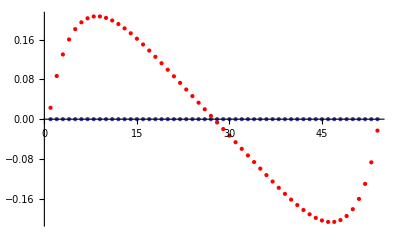

0.0881619

```mathematica
(*Poisson solver that implements the first part of the algorithm described below - it represents the Laplacian as a matrix operator then inverts it. Any solution to Poisson's equation is now found by multiplying the inverse matrix by the (forcing function ρ? idk if you can call it that)*)
(*This is a symmetric finite difference method to solve the Poisson Equation*) 
(*en.wikipedia.org/wiki/Discrete_Poisson_equation*)
Clear[MM,NN, ϵ,λ] 

stepSize=1;
MM= 55;(*Increases accuracy*)
NN=55;(*Pulls it back*)


(*construct D, the matrix operator that corresponds to the Laplacian. This is a 9 point stencil*)
periodicblock[a_,b_]:=a IdentityMatrix[MM-1]+DiagonalMatrix[Table[b,{i,0,MM-3}],1]+DiagonalMatrix[Table[b,{i,0,MM-3}],-1]+DiagonalMatrix[{b},-MM+2]+DiagonalMatrix[{b},MM-2];
asymmetricblock[a_,b_,c_]:=a IdentityMatrix[MM-1]+DiagonalMatrix[Table[b,{i,0,MM-3}],1]+DiagonalMatrix[{b},-MM+2]+DiagonalMatrix[Table[c,{i,0,MM-4}],2]+DiagonalMatrix[{c,c},-MM+3];
m1 = periodicblock[-2./3,-1/6];
m2 = periodicblock[10/3,-2/3];
m3 =KroneckerProduct[DiagonalMatrix[Join[Table[1,{i,1,NN}],{0}],0],m2];
m4 =KroneckerProduct[DiagonalMatrix[Join[Table[1,{i,1,NN-1}],{0}],1],m1];
m5 =KroneckerProduct[DiagonalMatrix[Join[Table[1,{i,1,NN-1}],{0}],-1],m1];
m6 =KroneckerProduct[DiagonalMatrix[{1},NN],m1];
m7=1/2 IdentityMatrix[MM-1];
m8 =KroneckerProduct[DiagonalMatrix[{0,1},-NN+1],-m7];
m9=KroneckerProduct[DiagonalMatrix[Join[Table[0,{i,1,NN}],{1}],0],m7];
m = m3+m4+m5+m6+m8+m9;
newm=m3+m4+m5;

inverseMatrix = Inverse[m];

ϵ=1;
λ=1000;
α = -2;
ω=(α π)/(MM stepSize);
ϕ=0;

n[x_,y_]:= Sin[ω y] ((ω^2(x - NN stepSize)^2)/2-1);(*If[x==Floor[1/2 NN stepSize],0/(4 π ϵ),0/(4 π ϵ)Cos[(x+y)]]*)(*Charge distribution*)
(*Von Neumann boundary conditions for the Poisson Equation*)
e1[y_]:=(0 - NN stepSize)Sin[ω y];(*Divergence of voltage at top edge of the grid at x=stepSize*)



(*Returns the boundary potentials in the correct form for the matrix solver, and shifts from ij indices to user inputted boundary conditions which are in xy*)
e[i_,j_]:=Which[
i==0,-N[e1[j stepSize]],
True,0
];

(*Defines the list with the charge distribution Subscript[ρ, ij] generated from the user, augmented with the boundary conditions *)
chargeVector  = Flatten[
Table[
stepSize^2 n[i stepSize,j stepSize],
{i,1,NN},
{j,1,MM-1}
]
];

exteriorPoints = Flatten[
Table[
  stepSize e[0,j] ,
{j,1,MM-1}
]
];

chargeVector = Join[chargeVector, exteriorPoints];
chargeVector2=chargeVector;
chargeVector=chargeVector-1/2 newm.chargeVector;
(*Calculates the potential*)
potential = inverseMatrix.chargeVector;

(*Gives the total potential in order to plot it. This includes the portion computed by the matrix solver and the periodic boundary. First it adds the calculated potential, then the periodic boundary which wasn't solved for*)
plotList  = Flatten[
Table[
{i stepSize,j stepSize,potential[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1
];
periodicEdge = 
Table[
{i stepSize,MM  stepSize,potential[[1 + (MM-1)(i-1)]]},
{i,1,NN}
];
plotList = Join[plotList, periodicEdge];

(*Generates the data on user inputted charge distribution to plot*)
chargeDistributionList  = Flatten[
Table[
{j stepSize,i stepSize,chargeVector2[[i + (NN-1)(j-1)]]},
{i,1,NN},
{j,1,MM-1}
],1
];

(*Plots the charge distribution, then the resulting potential*)
ListPlot3D[chargeDistributionList, PlotLabel->"Charge Distribution", PlotRange->All]
ListPlot3D[plotList,PlotRange->All,PlotLabel->"Calculated Electric Potential",PlotRange->All]

(*This plots the analytic solution for the test case*)
v[x_,y_]:=(x - NN stepSize)^2/2 Sin[ω y];
Plot3D[v[x,y],{x,0,NN stepSize},{y,0,MM stepSize},PlotLabel->"Analytic Electric Potential",PlotRange->All]


frontPlot1= ListPlot[
Table[
{ j stepSize,v[0,j stepSize]},
{j,1,MM-1}
]
];
frontPlot2 = ListPlot[
tempList  = Table[
{ j stepSize,potential[[j ]]},
{j,1,MM-1}
], PlotStyle->Red
];
Show[frontPlot1,frontPlot2,PlotRange->All](*Front edges*)

backPlot1= ListPlot[
Table[
{ j stepSize,v[NN stepSize,j stepSize]},
{j,1,MM-1}
]
];
backPlot2 = ListPlot[
tempList  = Table[
{ j stepSize,potential[[j + (NN-1)(MM-1) ]]},
{j,1,MM-1}
], PlotStyle->Red
];
Show[backPlot1,backPlot2,PlotRange->All]
 (*Back edges*)

helper[i_,j_]:=If[v[i stepSize, j stepSize]≠0,Abs[(potential[[j + (MM-1)(i-1)]]-v[i stepSize, j stepSize])/v[i stepSize, j stepSize]
],
0
]
error = Total[
Flatten[
Table[
helper[i,j],
{i,1,NN},
{j,1,MM-1}
]
]
];
error/(NN MM)
```